Solution to parts 1 and 2:

# 1) Background [easy]

## 1a) Einstein equations

-Graphics-

-Graphics-

```mathematica
coord = {t,x,y,z};
metric = DiagonalMatrix[{-1,a[t]^2,a[t]^2,a[t]^2}]
```

{{-1,0,0,0},{0,a[t]^2,0,0},{0,0,a[t]^2,0},{0,0,0,a[t]^2}}

```mathematica
<<(NotebookDirectory[]<>"diffgeo.m");
```

$Aborted

-Graphics-

```mathematica
lhs=(RicciTensor-1/2 metric RicciScalar//Simplify)[[1,1]]
```

(3 a'[t]^2)/a[t]^2

-Graphics-

```mathematica
(*-Graphics-*)ddphi=covariant[covariant[ϕ[t]]]
```

{{ϕ''[t],0,0,0},{0,-a[t] a'[t] ϕ'[t],0,0},{0,0,-a[t] a'[t] ϕ'[t],0},{0,0,0,-a[t] a'[t] ϕ'[t]}}

```mathematica
(*-Graphics-*)Tr[Inverse[metric].ddphi]
```

-(3 a'[t] ϕ'[t])/a[t]-ϕ''[t]

## 1b) Solving the equations numerically

-Graphics-

```mathematica
V[x_]=1/2 m^2 x^2;
```

```mathematica
eqs={√3 Mp a0'[t]==a0[t] √(1/2 ϕ0'[t]^2+V[ϕ0[t]]),ϕ0''[t]+3 a0'[t]/a0[t] ϕ0'[t]+V'[ϕ0[t]]==0};
sb0={Mp->1,m->1};
```

```mathematica
sls=NDSolve[(eqs/.sb0)~Join~{ϕ0[0]==95/10,ϕ0'[0]==-√(2/3),a0[0]==1},{ϕ0[t],a0[t]},{t,0,500}]
```

{{ϕ0[t]→InterpolatingFunction[{{0., 500.}}, <>][t],a0[t]→InterpolatingFunction[{{0., 500.}}, <>][t]}}

```mathematica
ϕ[t_]=ϕ0[t]/.sls[[1]];
a[t_]=a0[t]/.sls[[1]];
```

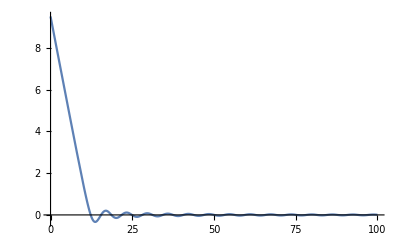

```mathematica
Plot[ϕ[t],{t,0,100},PlotRange->All]
```

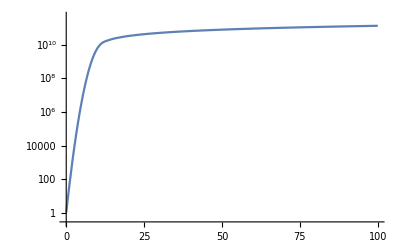

```mathematica
LogPlot[a[t],{t,0,100},PlotRange->All]
```

## 1c) Comparison with slow roll

-Graphics-

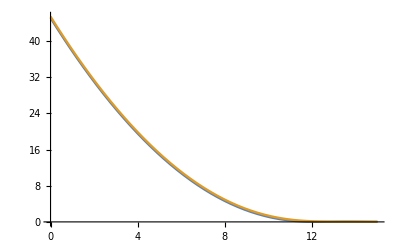

```mathematica
Plot[{1/2 ϕ[t]^2,3(a'[t]/a[t])^2},{t,0,15},PlotRange->All]
```

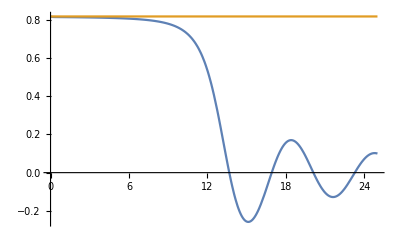

```mathematica
Plot[{-ϕ'[t],√(2/3)},{t,0,25},PlotRange->All]
```

## 1d) Comparison with matter domination

-Graphics-

```mathematica
α=2/3;
```

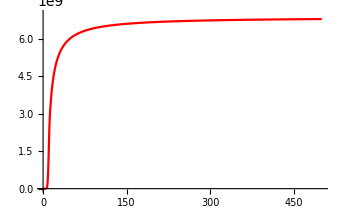

```mathematica
Plot[a[t]/t^α,{t,0,500},PlotStyle->Red,PlotRange->{0,7 10^9}]
```

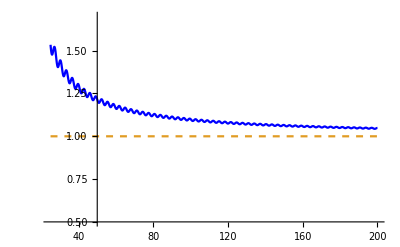

```mathematica
Plot[{1/α a'[t]/a[t] t,1},{t,25,200},PlotRange->{1/2,1.7},PlotStyle->{Blue,Dashed},PlotPoints->100]
```

# 2) Fluctuations [medium]

-Graphics-

```mathematica
ηmax=NIntegrate[1/a[t],{t,0,100}]-1/100000;
```

```mathematica
slt=NDSolve[{t0'[η]==a[t0[η]],t0[0]==0},t0[η],{η,0,ηmax}][[1]];
```

```mathematica
Unprotect[t];
t[η_]=t0[η]/.slt;
```

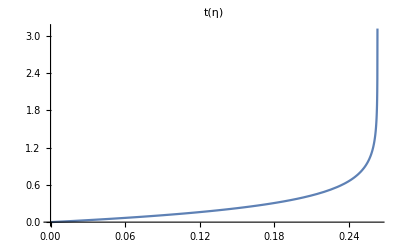

```mathematica
Plot[t[η],{η,0,ηmax},PlotRange->All,PlotLabel->"t(η)"]
```

-Graphics-

```mathematica
H[t_]=a'[t]/a[t];
f[η_]=a[t[η]]^2 ϕ'[t[η]]^2/H[t[η]]^2;
```

-Graphics-

```mathematica
ϵ=1/10^4;
Clear[spec];
spec[k0_]:=spec[k0]=ζk/.NDSolve[{D[f[η]D[ζk[η],η],η]+f[η]k^2 ζk[η]==0,ζk[ϵ]==Exp[I k ϵ]/(√(2 f[ϵ] k)),ζk'[ϵ]==D[Exp[I k η]/(√(2 f[η] k)),η]/.η->ϵ}/.k->k0,ζk,{η,ϵ,ηmax}][[1]]
```

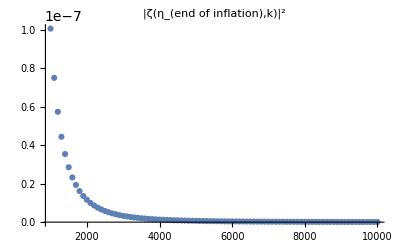

```mathematica
(*Table[{kk,Abs[spec[kk][ϵ]]^2 kk},{kk,1/20,7,1/20}]//ListPlot*)
ListPlot[Table[{kk,Abs[spec[kk][ηmax]]^2 },{kk,1000,10000,100}],PlotRange->All,PlotLabel->"|ζ(η_(end of inflation),k)|^2"]
```

-Graphics-

```mathematica
Clear[ηstar];
ηstar[k0_]:=ηstar[k0]=η/.FindRoot[a[t[η]] H[t[η]]-k0,{η,ηmax-1/10000}][[1]];
Amp[k0_]:=1/2 H[t[ηstar[k0]]]^4/ϕ'[t[ηstar[k0]]]^2 1/k0^3;
```

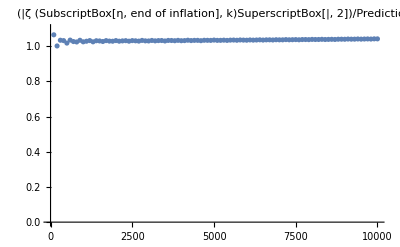

```mathematica
(*Table[{kk,Abs[spec[kk][ϵ]]^2 kk},{kk,1/20,7,1/20}]//ListPlot*)
ListPlot[Table[{kk,Abs[spec[kk][ηmax]]^2/Amp[kk] },{kk,100,10000,100}],PlotLabel->"(|ζ (SubscriptBox[η, end of inflation], k)SuperscriptBox[|, 2])/Prediction",PlotRange->{0,1.1}]
```